```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

Remove::rmnsm: There are no symbols matching ""Global`*"". ButtonBox["»", Appearance->{Automatic, None}, BaseStyle->"Link", ButtonData:>"paclet:ref/message/Remove/rmnsm", ButtonNote->"Remove::rmnsm"]

```mathematica
SetDirectory["~/Work/code/sim/testBench2/analyze"]
```

/home/andrew/Work/code/sim/testBench2/analyze

```mathematica
dat=Import["AllSpins.txt","Table"];
(*originGS=Import["gsorigin.dat","Table"];*)
Hangles=Import["field_angles.dat","Table"];
```

Import::nffil: File not found during Import.

```mathematica
nspins=(Length[dat])/4
spins=Table[{0,0,0},{i,1,nspins}];
```

9

```mathematica
Length[Hangles]
```

0

```mathematica
Do[spins[[i,1]]=dat[[4i-2]];
spins[[i,2]]=dat[[4i-1]];
spins[[i,3]]=dat[[4i]],{i,1,nspins}]
```

Check (the last) spin configuration against the file.

```mathematica
spins[[1]]//MatrixForm
```

(-0.109149 | 0.12822 | 0.985721
-0.495157 | -0.86192 | 0.109149
0.86192 | -0.490564 | -0.12822)

Check the Byron relationship

```mathematica
tol=10^-6;
Do[Print["config",i-1," check a ",If[spins[[i,1,1]]+spins[[i,2,3]]<tol,0,"oops"], 
" check e ",
If[ spins[[i,2,2]]+spins[[i,3,1]]<tol,0,"oops"],
" check d ",
If[spins[[i,2,1]]+spins[[i,1,3]]+spins[[i,3,2]]<(tol),0,"oops"]],{i,1,nspins}];
```

config0 check a 0 check e 0 check d 0

config1 check a 0 check e 0 check d 0

config2 check a 0 check e 0 check d 0

config3 check a 0 check e 0 check d 0

config4 check a 0 check e 0 check d 0

config5 check a 0 check e 0 check d 0

config6 check a 0 check e 0 check d 0

config7 check a 0 check e 0 check d 0

config8 check a 0 check e 0 check d 0

Now let’s take a look at what θ and ϕ values Andrew’s configurations correspond to.

tan ϕ = b/a (= sinθ sinϕ / sinθ cosϕ = y/x)
ArcTan[x,y]
cosθ=c

```mathematica
theta=Table[0,{i,1,nspins}];
phi=Table[0,{i,1,nspins}];
Do[theta[[i]]=ArcCos[spins[[i,1,3]]];
phi[[i]]=ArcTan[spins[[i,1,1]],spins[[i,1,2]]],{i,1,nspins}]
```

```mathematica
Hangles[[1,2]]
```

Part::partd: Part specification $Failed⟦1,2⟧ is longer than depth of object.

$Failed⟦1,2⟧

```mathematica
??If
```

RowBox[{"If", "[", RowBox[{StyleBox["condition", "TI"], ",", StyleBox["t", "TI"], ",", StyleBox["f", "TI"]}], "]"}] gives StyleBox["t", "TI"] if StyleBox["condition", "TI"] evaluates to True, and StyleBox["f", "TI"] if it evaluates to False. 
RowBox[{"If", "[", RowBox[{StyleBox["condition", "TI"], ",", StyleBox["t", "TI"], ",", StyleBox["f", "TI"], ",", StyleBox["u", "TI"]}], "]"}] gives StyleBox["u", "TI"] if StyleBox["condition", "TI"] evaluates to neither True nor False.

Attributes[If]={HoldRest,Protected}

```mathematica
π/4//N
```

0.785398

```mathematica
nspins
```

9

```mathematica
(*Do[If[theta[[i]]≤π/2,tmp=2*(π/2-theta[[i]]);th0=theta[[i]];theta[[i]]=th0+tmp,],{i,1,nspins,1}]*)
```

```mathematica
(*Do[If[phi[[i]]>π/4,tmp=2*(π/4-phi[[i]]);ph0=phi[[i]];phi[[i]]=ph0+tmp,],{i,1,nspins,1}]*)
```

```mathematica
Bound[ϕ_]:=If[Cos[4 ϕ]==1,π/3,ArcSin[√((4-√(16-6(1-Cos[4 ϕ])))/(1-Cos[4ϕ]))]]
```

```mathematica
marker1=Graphics[{RGBColor[0.22,0.6,0.32],Disk[]}];
marker2=Graphics[{RGBColor[0.13,0.83,1],Disk[]}];
```

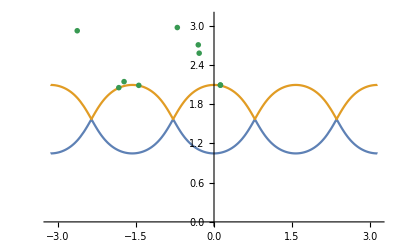

```mathematica
(*gsPlot=ListPlot[originGS,PlotStyle->Orange];*)
confPlot=ListPlot[Transpose[{phi,theta}],Frame->{True,True,False,False},FrameLabel->{"ϕ","θ"},Axes->False,PlotRangePadding->Automatic,PlotMarkers->{marker1,0.015}];
(*actGSPlot=ListPlot[actualGS,PlotStyle->Blue,PlotMarkers->{"X",20}];*)
boundPlot=Plot[{Bound[ϕ],π-Bound[ϕ]},{ϕ,-π,π},PlotRange->{{-180Degree,180Degree},{0,π}}];
Show[boundPlot,confPlot]
```

```mathematica
animation=Manipulate[Show[boundPlot,ListPlot[{{phi[[i]],theta[[i]]}}],ListPlot[{{Hangles[[i,1]],Hangles[[i,2]]}},PlotStyle->{Red}],ImageSize->{700,500}],{i,1,nspins,1},ContentSize->{700,500},AutorunSequencing->{{10,10}}]
```